```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab4

```mathematica
poly = Import["test2c.txt","Table"][[1]]
```

{-4.31336×10^17,-3.32095×10^16,5.03937×10^18,1.01377×10^17,-2.76356×10^19,8.37396×10^17,9.46413×10^19,-7.11006×10^18,-2.27158×10^20,2.61396×10^19,4.06554×10^20,-6.12823×10^19,-5.63588×10^20,1.02922×10^20,6.20551×10^20,-1.31029×10^20,-5.522×10^20,1.307×10^20,4.01991×10^20,-1.04339×10^20,-2.41469×10^20,6.76159×10^19,1.20388×10^20,-3.59141×10^19,-5.00047×10^19,1.57347×10^19,1.73383×10^19,-5.70854×10^18,-5.02077×10^18,1.71823×10^18,1.21311×10^18,-4.29143×10^17,-2.44009×10^17,8.88129×10^16,4.07121×10^16,-1.51836×10^16,-5.60446×10^15,2.13576×10^15,6.33007×10^14,-2.4528×10^14,-5.80038×10^13,2.28544×10^13,4.28412×10^12,-1.70148×10^12,-2.33533×10^11,1.16948×10^11,2.35379×10^10,1.55187×10^9,3.10213×10^9,1.5747×10^9,4.0825×10^8,9.18668×10^7,4.06569×10^7,-2.82611×10^6,-3.6861×10^6,-3.03873×10^6,-232040,-170479,-53132.1,-6345.69,-1598.49,-315.978,-16.3296,-3.27873,0.156244}

```mathematica
LagrangePolynom = ∑_(k=1)^(Length@poly) poly[[k]]*x^(Length@poly-k)
```

0.156244-3.27873 x-16.3296 x^2-315.978 x^3-1598.49 x^4-6345.69 x^5-53132.1 x^6-170479 x^7-232040 x^8-3.03873×10^6 x^9-3.6861×10^6 x^10-2.82611×10^6 x^11+4.06569×10^7 x^12+9.18668×10^7 x^13+4.0825×10^8 x^14+1.5747×10^9 x^15+3.10213×10^9 x^16+1.55187×10^9 x^17+2.35379×10^10 x^18+1.16948×10^11 x^19-2.33533×10^11 x^20-1.70148×10^12 x^21+4.28412×10^12 x^22+2.28544×10^13 x^23-5.80038×10^13 x^24-2.4528×10^14 x^25+6.33007×10^14 x^26+2.13576×10^15 x^27-5.60446×10^15 x^28-1.51836×10^16 x^29+4.07121×10^16 x^30+8.88129×10^16 x^31-2.44009×10^17 x^32-4.29143×10^17 x^33+1.21311×10^18 x^34+1.71823×10^18 x^35-5.02077×10^18 x^36-5.70854×10^18 x^37+1.73383×10^19 x^38+1.57347×10^19 x^39-5.00047×10^19 x^40-3.59141×10^19 x^41+1.20388×10^20 x^42+6.76159×10^19 x^43-2.41469×10^20 x^44-1.04339×10^20 x^45+4.01991×10^20 x^46+1.307×10^20 x^47-5.522×10^20 x^48-1.31029×10^20 x^49+6.20551×10^20 x^50+1.02922×10^20 x^51-5.63588×10^20 x^52-6.12823×10^19 x^53+4.06554×10^20 x^54+2.61396×10^19 x^55-2.27158×10^20 x^56-7.11006×10^18 x^57+9.46413×10^19 x^58+8.37396×10^17 x^59-2.76356×10^19 x^60+1.01377×10^17 x^61+5.03937×10^18 x^62-3.32095×10^16 x^63-4.31336×10^17 x^64

```mathematica
f = Cos[(x^5-x+3+2^(1/3))] + ArcTan[(x^3-5 √2 *x - 4)/(√6*x + √3)] + 1.8;
```

```mathematica
f /. x->0
```

0.200655

```mathematica
Cos[(x^5-x+3+2^(1/3))] /. x->0 // N
```

-0.437186

```mathematica
ArcTan[(x^3-5 √2 *x - 4)/(√6*x + √3)] /. x-> 0 //N
```

-1.16216

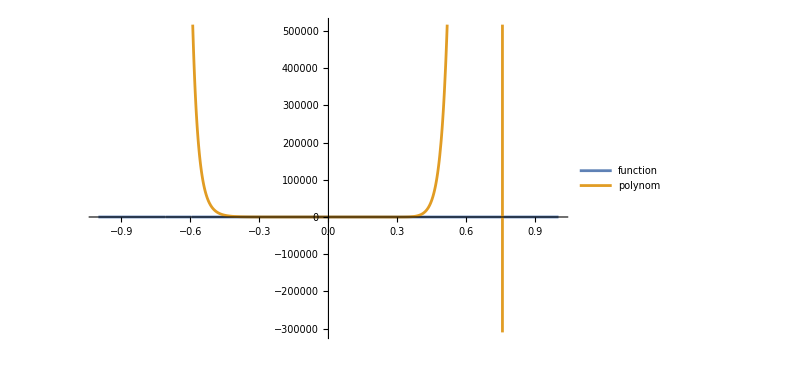

```mathematica
Plot[{f, LagrangePolynom},{x,-1,1},ImageSize->600,PlotLegends->{"function", "polynom"}]
```

```mathematica
f=((x-1)(x-2)(x-3))/((0-1)(0-2)(0-3)) + ((x)(x-2)(x-3))/((1-2)(1-3))E +((x)(x-1)(x-3))/((2)(2-1)(2-3))E^2 + ((x)(x-1)(x-2))/((3)(3-1)(3-2))E^3 // N //Expand
```

1.+1.93311 x-1.06036 x^2+0.845536 x^3

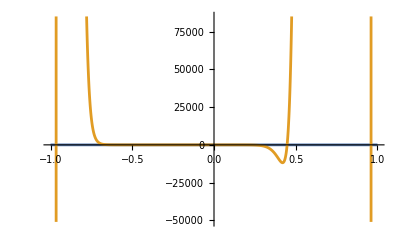

```mathematica
Plot[{E^x, LagrangePolynom},{x,-1,1}]
```

```mathematica
((x-1)(x-2)(x-3))/((0-1)(0-2)(0-3)) +  ((x)(x-2)(x-3))/((1-2)(1-3))E + ((x)(x-1)(x-3))/((2)(2-1)(2-3))E^2 +((x)(x-1)(x-2))/((3)(3-1)(3-2))E^3// Expand // N
```

1.+1.93311 x-1.06036 x^2+0.845536 x^3

```mathematica
(x-1)(x-2)//Expand
```

2-3 x+x^2

```mathematica
0*x^36+0*x^35+0*x^34+0*x^33+0*x^32+0*x^31+0*x^30+0*x^29+0*x^28+0*x^27+0*x^26+0*x^25+0*x^24+0*x^23+0*x^22+0*x^21+0*x^20+0*x^19+-5.95069 * 10^-11*x^18+5.64835* 10^-9*x^17+-2.46864* 10^-7*x^16+6.58669* 10^-6*x^15+-0.00011993*x^14+0.00157794*x^13+-0.0154962*x^12+0.115689*x^11+-0.66253*x^10+2.91581*x^9+-9.81654*x^8+24.9982*x^7+-47.2285*x^6+64.1918*x^5+-59.7036*x^4+34.6696*x^3+-9.96789*x^2+-0.0935224*x+1.27522  /. x->6.79
```

-342.13

```mathematica
0.7*(-6*0.3+4) + (1-0.7)(-3*0.3 + 2)
```

1.87

```mathematica
0.7*0.3 + 0.7 + 0.3 +1
```

2.21

```mathematica
9.02501 - Exp[2.2]
```

-3.49943×10^-6

```mathematica
0.2^11 Exp[2]
```

1.51328×10^-7

```mathematica
(n+1)(2^{n-1}*(n-1)*(n-1)+1) // Expand
```

{1+2^(-1+n)+n+2^(-1+n) n-2^n n+2^(-1+n) n^2-2^n n^2+2^(-1+n) n^3}